# ThermoFAST64 examples

The ThermoFAST64 package provides a Mathematica interface to the subroutines of the ThermoFAST64 DLL, as well as some extra functionality.

## Installing the paclet

The ThermoFAST64 package is distributed in the form of a paclet, which is essentially a zip file containing all the necessary files. To begin using a paclet, it must first be installed. This can be done by running the following (after modifying the file path appropriately; Insert > File Path… is useful here):

```mathematica
PacletInstall["path/to/ThermoFAST64.paclet"]
```

If installation was successful, running the following should give similar output:

```mathematica
p=PacletObject["ThermoFAST64"]
```

PacletObject[…]

```mathematica
Information[p]
```

Paclet

A given version of the paclet only needs to be installed once, after which the package will be available as discussed in the following section.

## Loading the package

After installing the paclet, the package needs to be loaded into the current session:

```mathematica
<<ThermoFAST64`
```

Note that because the package is now coming from an installed paclet, there is no longer any need to modify $Path as was done in earlier releases.

The remainder of this notebook gives an overview of the package functionality.

## Pressure-Temperature Flash calculation

Most of the subroutines in the ThermoFAST64 dll are based on the pT-flash calculation, so it is a natural starting point for exploring the package.

```mathematica
?FlashPTSolve
```

### Defining the feed

The first step is to specify the mixture and model settings in the form of a FeedModel:

```mathematica
?FeedModel
```

In the simplest case, a feed can be specified by giving the components and their molar weights:

```mathematica
feed=FeedModel[{"Methane"->0.7,"Benzene"->0.3}]
```

FeedModel[…]

The first argument to FeedModel specifies the fractions of each component, and assumes that both components are “solid-formers”, i.e. they assumed to form a solid phase at suitably low temperatures.

Solid formation can be prevented on a component-by-component basis by adding False to the right-hand side. For example, this would prevent benzene from being able to form a solid phase:

```mathematica
FeedModel[{"Methane"->0.7,"Benzene"->{0.3,False}}]
```

FeedModel[…]

In the above examples, suitable default values for all models and parameters are chosen automatically. For advanced users, it is possible to choose model values manually:

```mathematica
Options[FeedModel]
```

{FluidModel→Automatic,SolidModel→Automatic,HydrateModel→Automatic,HydrateType→Automatic,TransportModel→Automatic}

### Specifying pressure and temperature

We next define the pressure and temperature. In ThermoFAST64, values may be specified as numbers, in which case they will be interpreted in units of Megapascals (pressure) or Kelvins (temperature).

```mathematica
p=2.;T=200.;
```

A nice feature of Mathematica is its built-in support for physical quantities, which makes it possible to specify values from other unit systems. Thus, e.g., the following definitions are equivalent to the above:

```mathematica
p=Quantity[2000,"Kilopascals"];T=Quantity[-73.15,"DegreesCelsius"];
```

### Running a flash calculation

We can now call the function:

```mathematica
res=FlashPTSolve[feed,p,T]
```

MultiphaseEquilibriumData[…]

### Output objects

The output of the above flash calculation is a MultiphaseEquilibriumData object containing information about the stable phase(s) for the given inputs. It contains one or more PhaseData objects describing each phase:

```mathematica
phases=res["Phases"]
```

{PhaseData[…],PhaseData[…]}

```mathematica
vapour=phases[[1]]
```

PhaseData[…]

```mathematica
solid=phases[[2]]
```

PhaseData[…]

### Accessing information about phases

The MultiphaseEquilibriumData and PhaseData objects encapsulate the data relevant to the thermodynamic state. To see what attributes are available, you can use Keys:

```mathematica
Keys[res]
```

{Description,Components,Phases}

```mathematica
Keys[vapour]
```

{Components,Molar Amount,Mass Amount,Molar Mass,Molar Density,Mass Density,Pressure,Temperature,Volume,Entropy,Internal Energy,Helmholtz Energy,Enthalpy,Gibbs Energy,Compressibility Factor,Heat Capacity Cv,Heat Capacity Cp,Speed Of Sound,Joule-Thomson Coefficient,Isothermal Throttling Coefficient,Isothermal Expansion Coefficient,Isentropic Expansion Coefficient,Volume Expansivity,Isothermal Compressibility,Isentropic Compressibility,Grueneisen Parameter,Lower Heating Value,Higher Heating Value,Wobbe Index,Viscosity,Thermal Conductivity,Phase Identification Parameter,Binary Thermodynamic Factor,Name,Phase Type,Molar Fraction,Fugacity,Fugacity Coefficient,Thermodynamic Factor}

```mathematica
solid[[1]]
```

<|Components→{Methane,Benzene},Molar Amount→0.299997 mol,Mass Amount→23.4333 kg,Molar Mass→0.0781118 kg/mol,Molar Density→12989.6 mol/m^3,Mass Density→1014.64 kg/m^3,Pressure→2. MPa,Temperature→200. K,Volume→0.0000769848 m^3/mol,Enthalpy→-50763. J/mol,Thermal Conductivity→0.36804 W/(m K),Saturation Pressure→0. MPa,Saturation Fluid Phi→1.,Subcooled Liquid Phi→8.06219×10^-6,Name→Solid Benzene,Phase Type→Solid,Key Component→Benzene,Molar Fraction→{0.,1.},Mass Fraction→{0.,1.},Fugacity→{Indeterminate MPa,2.99016×10^-6 MPa},Fugacity Coefficient→{Indeterminate,1.49508×10^-6}|>

```mathematica
Keys[solid]
```

{Components,Molar Amount,Mass Amount,Molar Mass,Molar Density,Mass Density,Pressure,Temperature,Volume,Enthalpy,Thermal Conductivity,Saturation Pressure,Saturation Fluid Phi,Subcooled Liquid Phi,Name,Phase Type,Key Component,Molar Fraction,Mass Fraction,Fugacity,Fugacity Coefficient}

```mathematica
solid["Fugacity Coefficient"]
```

{Indeterminate,1.49508×10^-6}

```mathematica
solid["Enthalpy"]
```

-50763. J/mol

## Other flash calculations

While the pT-flash is the main workhorse, several other flash calculations are also supported:

```mathematica
?FlashTDSolve
```

```mathematica
?FlashPHSolve
```

Dew and bubble point functions are also available:

```mathematica
?DewPSolve
```

```mathematica
?BubbleTSolve
```

## Single-phase calculations

Functions like FlashPTSolve attempt to compute a thermodynamically stable multiphase equilibrium, which is intended to represent a physically plausible state of the given mixture. However, it is sometimes desirable to calculate states which are not thermodynamically stable. In flash calculations this is already somewhat available in the way one can “turn off” solid formation for specific components of the mixture. The functions below take this further allow the calculation of single fluid and pure solid phases.

The function FluidPhase calculates a hypothetical single fluid phase state for a feed at a given pressure and temperature:

```mathematica
?FluidPhase
```

The PhaseHint option allows the desired type of fluid (liquid or vapour) to be specified:

```mathematica
Options[FluidPhase]
```

{PhaseHint→Automatic}

```mathematica
$PhaseHints
```

{Automatic,Vapour,Liquid,Vapour Or Nearest Maximum,Liquid Or Nearest Minimum}

Similarly, PureSolidPhases will return a list of pure solid phases for all the components in the mixture:

```mathematica
?PureSolidPhases
```

As a convenience there are also functions to evaluate the fugacity coefficients ϕ_i corresponding the above phases:

```mathematica
?FluidLogPhi
```

```mathematica
?SolidLogPhi
```

```mathematica
phi[p_,T_]:=SolidLogPhi[FeedModel[{"Benzene"->1},FluidModel->"Pure Fluid Reference",SolidModel->"Helmholtz"],p,T]
```

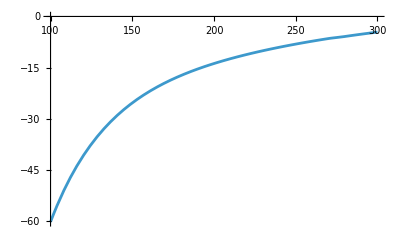

```mathematica
Plot[phi[2.,T],{T,100,300}]
```

## Fugacity coefficients

## Solid and hydrate formation **COMING SOON**

** COMING SOON **

### Solid formation

```mathematica
mixture={"Methane"->0.7,"Benzene"->0.3};
p=Quantity[2,"Megapascals"];
```

```mathematica
SolidTransitionTemperatures[mixture,p]
```

### Hydrate formation

```mathematica
mixture={"Methane"->0.7,"Water"->0.3};
p=Quantity[2,"Megapascals"];
T=Quantity[200,"Kelvins"];
```

```mathematica
HydrateFormationTemperature[mixture,p]
```

```mathematica
HydrateFormationPressure[mixture,T]
```

### General phase transitions

The following functions find all phase transitions occurring within a given range of temperatures or pressures:

```mathematica
mixture={"Methane"->0.9,"Benzene"->0.1};
```

```mathematica
p=Quantity[2,"Megapascals"];
{Tmin,Tmax}=Quantity[{30,300},"Kelvins"];
```

```mathematica
IsobaricPhaseTransitions[mixture,p,{Tmin,Tmax}]
```

```mathematica
{pmin,pmax}=Quantity[{0.01,10},"Megapascals"];
T=Quantity[200,"Kelvins"];
```

```mathematica
IsothermalPhaseTransitions[mixture,{pmin,pmax},T]
```

## Phase diagrams **COMING SOON**

Although still a work in progress, the ThermoFAST64 package has several functions for generating phase diagrams that can be useful.

### PlotPhaseBoundaries

This function identifies transitions within the given pressure and temperature ranges, linearly sampling points according to the value of the PlotPoints option (default value is 20). It is useful for obtaining a “quick and dirty” visualization of the phase behaviour for a mixture.

```mathematica
mixture=With[{x=0.001},{"Normal Hydrogen"->1-x,"Nitrogen"->x}];
```

```mathematica
PlotPhaseBoundaries[mixture,{0.1,8},{30,55}]
```

### ListPlotPhaseBoundaries

This function is similar to PlotPhaseBoundaries but instead of pressure and temperature ranges, it takes explicit lists of values. This allows the resolution to be more carefully attuned to the structure of the phase diagram, avoiding unnecessary computation and making it more useful for generating high resolution phase diagram visualizations.

```mathematica
mixture=With[{x=0.001},{"Normal Hydrogen"->1-x,"Nitrogen"->x}];
```

```mathematica
pValues=Join[Range[0.1,2,0.1],Range[2.5,8,0.5]];
TValues=Join[Range[30,43,1],Range[43.1,45,0.1],Range[45,55,1]];
```

```mathematica
ListPlotPhaseBoundaries[mixture,pValues,TValues,Joined->True]
```

### PhaseBoundaryPoints

It is sometimes useful to be able to generate the phase boundary points rather than a plot. E.g. this is helpful when there are many different phase boundaries and you want to consider only a subset of them. In this case the function PhaseBoundaryPoints may useful:

```mathematica
mixture=With[{x=0.001},{"Normal Hydrogen"->1-x,"Nitrogen"->x}];
```

```mathematica
pValues=Join[Range[0.1,2,0.1],Range[2.5,8,0.5]];
TValues=Join[Range[30,43,1],Range[43.1,45,0.1],Range[45,55,1]];
```

```mathematica
PhaseBoundaryPoints[mixture,pValues,TValues]
```

## Low-Level subroutine wrappers **DESCRIPTION TO BE ADDED**